# Defect Modular Bootstrap

## When the modular matrix has degeneracies modular bootstrap can only do so much to predict the the topological lines of the theory. Here we use a version of Breadth First Search to resolve the ambiguities.

## Modular Bootstrap

We will do this example on the folded Tricritical Ising CFT, but the parameters will be documented so that one can change them.

### Defining Folded Tricritical Ising Modular Data

Time:   0.625351

Time:   0.028045

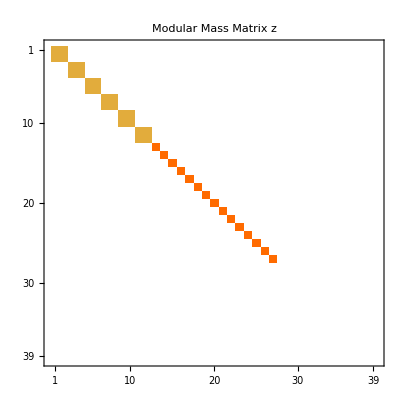

```mathematica
(* Autosave because I've been burnt before *)
SetOptions[$FrontEnd,AutoSaveFrequency->1]

(* A Timing Function *)
SetAttributes[Time,HoldFirst]
Time[x_]:=With[{res=AbsoluteTiming[x]},Echo[res[[1]],"Time: "];res[[2]]];

(* Define Tricritical Ising Parameters *)
FoldedMinimalModularData[p_:5,pp_:4]:= Module[
{cv,hv,sv,tv,H,i,ho,t,sMaker,s,nH,HIndex,svMat,tv2,twist},
cv=1-6(p-pp)^2/(p pp);(*//Echo[#,"c = "]&;*)
hv[r_,s_]:=hv[r,s]=((p r - pp s)^2-(p - pp)^2)/(4 p pp);
sv[a_,b_]:=sv[a,b]=2 (2/(p pp))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/pp a[[1]] b[[1]]]Sin[π pp/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=tv[a,e]=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(pp-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[pp], Table[{pp/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];

(* Labels of folded Minimal Model primaries under the fixed point chiral algebra *)
i=({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);

(* Their Conformal Weights *)
ho[a_]:=ho[a]=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;

(* Modular T-Matrix *)
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;

(*── Precomputed sv/tv tables for H×H ──────────────────────────────*)
nH=Length[H];
HIndex=AssociationThread[H->Range[nH]];
svMat=Table[sv[H[[a]],H[[b]]],{a,nH},{b,nH}];
tv2=Table[tv[H[[a]]]^2,{a,nH}];
twist[a1_,b1_]:=twist[a1,b1]=svMat[[HIndex[a1]]].(tv2*svMat[[All,HIndex[b1]]]);

(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:=sMaker[a,b]=Module[
{a1=a[[1]],a2=a[[2]],a3=a[[3]],b1=b[[1]],b2=b[[2]],b3=b[[3]]},
Which[a3==0&&b3==0,sv[a1,b1] sv[a2,b2]+sv[a1,b2] sv[a2,b1],
a3==0&&Abs[b3]==1,sv[a1,b1] sv[a2,b1],
Abs[a3]==1&&b3==0,sv[a1,b1] sv[a1,b2],
Abs[a3]==1&&Abs[b3]==1,1/2 sv[a1,b1]^2,
Abs[a3]==1&&Abs[b3]==2,1/2 a3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==1,1/2 b3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==2,1/8 a3 b3 twist[a1,b1] Exp[π ⅈ (hv@@a1+hv@@b1-cv/12)],
True,0]
];

s=Simplify[Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}],ComplexityFunction->LeafCount];
{s,t,i}
];
{s,t,i}=(Clear[s,t,i];FoldedMinimalModularData[5,4])//Time;

(* Modular Mass Matrix *)
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];//Time;
MatrixPlot[z,PlotLabel->"Modular Mass Matrix z"]
```

### Obtaining Modular Bootstrap Equations

```mathematica
SolveModularBootstrap[z_,s_]:=Module[
{X,x,nz, st=ConjugateTranspose[s],m,coeff,A, eqn,multipliers,basis},
Needs["math4ti2`"];

(* Get Nonzero positions on the Mass Matrix and replace them with variables *)
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=st. ReplacePart[z,Thread[nz->X]] . s//Flatten;

(* Extract the coefficients for each variable in the S transformed Mass Matrix *)
coeff= CoefficientArrays[m,X][[2]]//Normal//N//Chop;

(* Pick the maximum number of independent equations and invert them *)
A=Chop@Inverse@N@coeff[[Flatten[FirstPosition[#,1]&/@DeleteCases[Chop@RowReduce@N@Transpose@coeff,{0..}]]]];

(* Plug them back in to the S-Transformed Modular Matrix to obtain constraints *)
m=Chop[N[coeff.A]].X;
A=RootApproximant[A];
eqn=DeleteDuplicates@Rationalize@Chop@Expand[#>=0&/@m];

(* Rescale any variables that need it so that the system has integer coefficients *)
multipliers=Min@Cases[eqn,(a_.*#)>=0:>a]^-1&/@X;
eqn=(#[[0]][Subtract@@#//ExpandAll,0])&/@(eqn/. Thread[X->multipliers*X]);

(* Use Z-Solve to find a basis of simple objects *)
basis =math4ti2`zsolve[eqn][[2]];

A. (multipliers*#)&/@basis //FullSimplify
];
families=Sort[SolveModularBootstrap[z,s],#1[[1]] <= #2[[1]]&];//Time
families//Transpose//MatrixForm
noninvertibleFamilies=Select[families,#[[1]]!=1&];
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

Time:   2.95819

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Resolving Ambiguities

As we can see from the answers above for part of the primaries the action of the defects is ambiguous and we really only know the trace. Yet we have a lot of data, perhaps enough to fully constrain the action on the primaries (up to a basis choice). To do this we will use fusion rules. These are highly constrained also simply by looking at the action in the nondegenerate primaries. Then we will search fusion rules for consistencies using a version of BFS.

### Defect Manipulations

Since we don’t need a really big matrix to store the action of the defects, we will instead opt to store them using a list of 1x1 and 2x2 matrices depending on which are ambiguous or not. So we can define an associative operation for the tensor product!!

```mathematica
(* Define a Defect Fusion Product Operation *)
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=Which[MatrixQ[#[[1]]]&&MatrixQ[#[[2]]],#[[1]].#[[2]],True,#[[1]]*#[[2]]]&/@Transpose[{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]

(* A couple of helper functions that can be applied to Lines *)
tr[x_]:=Which[MatrixQ[x],Tr[x],True,x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],True,1/x];
dual[x_]:=Which[MatrixQ[x],ConjugateTranspose[x],True,Conjugate[x]];
SuperDagger[x_]:=dual/@x;
ShowLine[L_]:=MatrixForm[MatrixForm/@L];

(* This mask tells us if the current primary is degenerate *)
degMask=Thread[families[[1]]!=1];
degPos=Flatten@Position[degMask,True];
nondegPos=Flatten@Position[Not/@degMask,True];
deg[x_]:=degMask[[x]];
degNum=Total@Boole@degMask;
primNum=Total@Boole@degMask;
famNum=Length@families;
familiesNondeg=families[[All,nondegPos]];
```

### Invertible Lines

```mathematica
GetInvertibleLines[]:=Module[
{i={{1,0},{0,1}},
a={{1,0},{0,-1}},
b={{0,1},{1,0}},
c={{0,1},{-1,0}},
L1,Lσ,Lχ},
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,a,a,a,c,c,a,a,c,c,a,c,c,c,c,-a};
{L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗Lχ⊗Lχ,Lχ,Lχ⊗Lχ⊗Lχ}
];

(* Extract the invertible Lines *)
Li=GetInvertibleLines[];
L=GetInvertibleLines[];
solvedFamilies=<|
1->{Li[[1]]},
2->{Li[[2]]},
3->Li[[3;;4]],
4->Li[[5;;6]],
5->Li[[7;;8]]
|>;
SolvedQ[x_Integer]:=KeyExistsQ[solvedFamilies,x];

(* Functions to create a defect with free variables and given traces, as well to extract the variables *)
l[traces_,var_]:= Array[Which[!deg[#],traces[[#]],deg[#],{{var[#,1]+ⅈ var[#,2] ,var[#,3]+ⅈ var[#,4] },{var[#,5]+ⅈ var[#,6],traces[[#]]-var[#,1]-ⅈ var[#,2]}}]&,Length@traces];
getVars[x_]:=x//Flatten//Variables;

(* Obtain a general Gauge Transformation that preserves the solved Lines *)
gaugeVars= getVars[L];
gaugeVarRules=Thread[gaugeVars!=0];
GetGeneralGaugeTransform[L_,gaugeVars_,gaugeVarRules_,var_:P]:=Module[{Lp,LpInvertibleQ,Lpp},
(* Build a General Gauge Transformation *)
Lp=Array[Which[!deg[#],1,deg[#],{{var[#,1] ,var[#,2] },{var[#,3],var[#,4]}}]&,famNum];
Lp=(Lp //.{Assuming[gaugeVarRules,ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@L]==0],Backsubstitution->True]]]});
Lpp=DeleteElements[Variables[Lp],gaugeVars];

(* Checks if Lp is invertible for a given numerical set of P variables *)
Module[{
vars=Table[Unique["p"],Length@Lpp],
varsg=Table[Unique["g"],Length@gaugeVars],
invertibleLp=And@@((Simplify@Not@Reduce[Or@@(Which[MatrixQ[#],Det[#]==0,True,#==0]&/@#)])&/@Lp)
},
invertibleLp=invertibleLp/.Thread[Lpp->vars]/.Thread[gaugeVars->varsg];
LpInvertibleQ:=Function@@{vars,Assuming[gaugeVarRules/.Thread[gaugeVars->varsg],Simplify[Evaluate[invertibleLp]]]}
];
{Lp,Lpp,LpInvertibleQ}
];
{Lp,Lpp,LpInvertibleQ} =GetGeneralGaugeTransform[L,gaugeVars,gaugeVarRules,P];

(* These are Queries for if a line is related by conjugation of invertible defects, or by a change of Gauge, or both *)
Clear[conjugateOrbit,NconjugateOrbit,leftOrbit,rightOrbit,gaugeNullSpace,fusionOrbit]
conjugateOrbit[x_,Li_:Li,gaugeVarRules_:gaugeVarRules]:=conjugateOrbit[x,Li,gaugeVarRules]=DeleteDuplicates[Simplify[#⊗x⊗(inv/@#),Assumptions->gaugeVarRules]&/@Li];
fusionOrbit[x_,L_:L,gaugeVarRules_:gaugeVarRules]:=fusionOrbit[x,L,gaugeVarRules]=DeleteDuplicates[Simplify[Flatten[Outer[#1⊗x⊗#2&,L,L,1,1],1],Assumptions->gaugeVarRules]];
NconjugateOrbit[x_,Li_:Li,gaugeVarRules_:gaugeVarRules]:=NconjugateOrbit[x]=DeleteDuplicates[Rationalize[N[Simplify[#⊗x⊗(inv/@#),Assumptions->gaugeVarRules]&/@Li]]];
ConjugateOrbitQ[x_,y_,Li_:Li]:=MemberQ[NconjugateOrbit[x],Rationalize@N[y]];
leftOrbit[x_,Li_:Li]:=leftOrbit[x,Li]=Rationalize@N[#⊗x]&/@Li;
LeftOrbitQ[x_,y_,Li_:Li]:=MemberQ[leftOrbit[x,Li],Rationalize@N[y]];
rightOrbit[x_,Li_:Li]:=rightOrbit[x,Li]=Rationalize@N[x⊗#]&/@Li;
RightOrbitQ[x_,y_,Li_:Li]:=MemberQ[rightOrbit[x,Li],Rationalize@N[y]];
OrbitQ[x_,y_,Li_:Li]:=Or[RightOrbitQ[x,y,Li],LeftOrbitQ[x,y,Li],ConjugateOrbitQ[x,y,Li]];

(* Calculates the nullspace of the Jacobian of Lp x - x Lp, and if it is empty then there is no gauge transformation *)
gaugeNullSpace[x_,y_,Lp_:Lp,Lpp_:Lpp]:=gaugeNullSpace[x,y,Lp,Lpp]=(NullSpace@Outer[D,Flatten[ExpandAll[#⊗x-y⊗#]],Lpp])&/@Lp;
GaugeQ[x_,y_,Lp_:Lp,Lpp_:Lpp,LpInvertibleQ_:LpInvertibleQ]:=Module[
{ns,dummies},
ns=gaugeNullSpace[x,y,Lp,Lpp];
Or@@(Which[
#==={},False,
Length@# ===Length@Lpp,True,
True,
dummies=Array[x,Length@#];
Assuming[Thread[Variables[{x,y,dummies}]!=0],Simplify[LpInvertibleQ@@(dummies.#)]]
]&/@ns)];

(* Combines all queries *)
OrbitGaugeQ[x_,y_,Li_:Li,Lp_:Lp,Lpp_:Lpp,LpInvertibleQ_:LpInvertibleQ]:=OrbitQ[x,y,Li]||GaugeQ[x,y,Lp,Lpp,LpInvertibleQ];

(* Solves system quietly ignoring the cases when parameters are undetermined *)
QuietSolve[eqn_,vars_]:=Quiet[Echo[vars];Solve[(eqn//.(((Conjugate[#] #)->Abs[#]^2)&/@vars)),vars],{Solve::svars,Solve::fulldim,Solve::ratnz}];
QuietSolveComplex[eqn_List,vars_]:=Module[{clauses,deduped,reduced,solutions},(*eqn is a list of And-clauses—deduplicate them cheaply using canonical form before doing any hard work*)clauses=DeleteDuplicates[Sort[List@@#]&/@eqn  (*sort equations within each clause for comparison*)];
(*Reduce each clause /independently:handles implied/redundant equations much better than Solve on the full Or*)reduced=Map[Quiet[Reduce[#,vars,Complexes],{Reduce::ratnz,Reduce::ztest}]&,clauses];
(*Drop clauses that reduced to False,then Solve the survivors*)reduced=DeleteCases[reduced,False];
solutions=Map[Quiet[Solve[#,vars,Complexes],{Solve::svars,Solve::fulldim,Solve::ratnz}]&,reduced];
Flatten[solutions,1]];

(* Cleans up some variables *)
CanonicalizeVars[list_]:=Array[i|->Module[{vars},
vars=getVars@list[[i]];
list[[i]]/.MapIndexed[#->#[[0]][i,#2[[1]]]&,vars]],
Length@list];

(* Given a defect with free variables, it outputs a list of the variables that are pure gauge *)
GaugeParams[x_]:=Module[
{vars=getVars@x},
Pick[vars,Simplify[GaugeQ[x,x/. #->z]&/@vars,Assumptions->Flatten[{Thread[vars!=0],z!=0}]]]
];
AllGaugeQ[x_]:=Flatten[First/@BooleanVariables[FunctionDomain[Flatten[x],Variables[x]]]]===Flatten[GaugeParams[x]];
```

### Search Fusion Rules

Since we can obtain some partial information for the fusion rules among defects belonging to each family we can extract and list them in the following

```mathematica
(* Takes a matrix M and a vector v and finds all possible nonnegative integer combinations of rows of M that sum to v *)
FindIntegerCombinations[M_,v_]:=Module[
{n=Length[M],m=Length[v],MT=Transpose[N[M]],ubounds, enumerate,results={}},

(* Use linear programming to estimate the maximum number a row can be added in a solution for v *)
ubounds=Table[Module[{sol},
sol=Quiet[LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]]
,{i,n}];

(* Explore the rest recursively until you hit zero *)
enumerate[rem_,idx_,current_]:=Which[idx>n,If[Chop[N[rem]]==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results
];
Clear[FindIntegerCombinationsCached];
FindIntegerCombinationsCached[M_,v_]:=FindIntegerCombinationsCached[M,v]=FindIntegerCombinations[M,v];
```

## Solving with Existing Lines

As we keep going through families with higher and higher quantum dimension we can use existing lines to constrain new ones. This is a variation of constrain with invertible lines, but this time it uses the full might of the already solved families. We will do an extra optimization. Since once a family is solved we know all the lines there and not just the traces,  this places a much stricter constraint on what the results of fusions can be other than their traces.

```mathematica
(* Find possible integer combinations for a defect with unknown variables *)
PossibleSimpleDecompositions[trace_]:=Module[
{vars=Variables[trace],indices},
Which[
Length[vars]==0,
FindIntegerCombinationsCached[families,trace],
True,
indices=Flatten@Position[trace, _?(FreeQ[#,Alternatives@@vars]&),{1},Heads->False];
FindIntegerCombinationsCached[families[[All,indices]],trace[[indices]]]
]
];

(* Uses trace equations and known lines to produce candidates for the unknown parameters *)
ReduceDecompositions[defect_,trace_,decompositions_]:=Or@@(decomp|->Module[
{sparseDecomp=SparseArray[decomp],indices},
indices=sparseDecomp["NonzeroPositions"][[All,1]];
Which[
(* If the fusion is in one family and it has been solved equate them cell by cell *)
And[Length[indices]==1,SolvedQ[indices[[1]]]],
BooleanConvert[Or@@(And@@DeleteCases[MapThread[Equal,{Flatten[defect],Flatten[#]}],True]&/@solvedFamilies[indices[[1]]]),"DNF"],
(* Otherwise equate their traces *)
True,
BooleanConvert[And@@DeleteCases[MapThread[Equal,{Flatten[trace],decomp.families},1],True],"DNF"]
]])/@decompositions;


ConstrainWithKnown[defect_,var_:x,L_:L,gaugeVars_:gaugeVars,gaugeVarRules_:gaugeVarRules]:=Module[
{vars=Variables[defect],products,traces,decompositions,result},

(* Calculate the possible fusion channels with the known defects *)
products=fusionOrbit[defect,L,gaugeVarRules];
traces=tr/@#&/@products;
decompositions=PossibleSimpleDecompositions/@traces;

(* Obtain a system of equations and reduce it *)
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=(defect//.#)&/@(QuietSolve[decompositions,vars]);

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,OrbitGaugeQ]
];
```

## Constraining with Dual Fusion

Each defect must fuse with its dual such that it produces the identity. In a unitary representation the dual is given by the conjugate transpose, and therefore we can impose this as a consistency condition as well.

```mathematica
(* Constrain using fusion with their dual *)
ConstrainWithDualFusion[defects_]:=Module[
{vars=Variables[defects],products,traces,decompositions,result},

(* Calculate Fusion among members of family *)
products=DeleteDuplicates[Simplify[Flatten[{((#⊗ SuperDagger[#]-Li[[1]])),((SuperDagger[#]⊗ #-Li[[1]]))}&/@defects,1],Assumptions->Thread[vars∈Reals]]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
Echo[decompositions];
result=DeleteDuplicates[Flatten[(defects//.#)&/@(QuietSolve[N[decompositions],vars]),1]];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,OrbitGaugeQ]
];
```

## Constraining with Self Fusion

The last condition we will impose is the fusion of the defects among themselves. In particular, if we have a collection of defects, their products should all have fusion decompositions in our fusion ring. This will help us pinpoint the remaining gauge degrees of freedom.

```mathematica
(* Constrain using fusion among thesemeves *)
ConstrainWithSelfFusion[defects_]:=Module[
{vars=Variables[defects],products,traces,decompositions,result},

(* Calculate Fusion among members of family *)
products=DeleteDuplicates[Flatten[Outer[#1⊗#2&,defects,defects,1,1],1]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=Flatten[(defects//.#)&/@(QuietSolve[N[decompositions],vars]),1];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,OrbitGaugeQ]
];
```

```mathematica
GaugeInvariantConstraints[L_,Lp_:Lp,Lpp_:Lpp,gaugeVarRules_:gaugeVarRules]:=Module[{gaugedL,orbitEqns},
(*The orbit equation:L'=Lp⊗L⊗Lp^{-1}*)
gaugedL=Simplify[Lp[[1]]⊗L⊗inv/@(Lp[[1]]),Assumptions->gaugeVarRules];

(*Equations saying L is fixed by the orbit,eliminate gauge params*)orbitEqns=And@@Flatten@MapThread[Equal,{Flatten[gaugedL],Flatten[L]}];
Echo[orbitEqns,And@@gaugeVarRules];
Eliminate[orbitEqns&&And@@gaugeVarRules,Lpp]]
```

```mathematica
SetAttributes[x,NHoldAll];
def=l[families[[7]],x];
res=ConstrainWithKnown[def]//Time;
(*ShowLine/@res*)
res=ConstrainWithDualFusion[res]//Time;
ShowLine/@res
res=ConstrainWithSelfFusion[res]//Time;
ShowLine/@res
```

{x[25,1],x[25,2],x[25,3],x[25,4],x[25,5],x[25,6],x[26,1],x[26,2],x[26,3],x[26,4],x[26,5],x[26,6],x[27,1],x[27,2],x[27,3],x[27,4],x[27,5],x[27,6],x[28,1],x[28,2],x[28,3],x[28,4],x[28,5],x[28,6],x[29,1],x[29,2],x[29,3],x[29,4],x[29,5],x[29,6],x[30,1],x[30,2],x[30,3],x[30,4],x[30,5],x[30,6],x[31,1],x[31,2],x[31,3],x[31,4],x[31,5],x[31,6],x[32,1],x[32,2],x[32,3],x[32,4],x[32,5],x[32,6],x[33,1],x[33,2],x[33,3],x[33,4],x[33,5],x[33,6],x[34,1],x[34,2],x[34,3],x[34,4],x[34,5],x[34,6],x[35,1],x[35,2],x[35,3],x[35,4],x[35,5],x[35,6],x[36,1],x[36,2],x[36,3],x[36,4],x[36,5],x[36,6],x[37,1],x[37,2],x[37,3],x[37,4],x[37,5],x[37,6],x[38,1],x[38,2],x[38,3],x[38,4],x[38,5],x[38,6],x[39,1],x[39,2],x[39,3],x[39,4],x[39,5],x[39,6]}

Time:   0.365149

{-1+x[1,1]^2+x[1,2]^2==1&&-1+x[1,3]^2+x[1,4]^2==1&&1+x[1,5]^2+x[1,6]^2==1&&√2 (x[1,5]+ⅈ x[1,6]+x[1,7]-ⅈ x[1,8])==0&&√2 (x[1,5]-ⅈ x[1,6]+x[1,7]+ⅈ x[1,8])==0&&1+x[1,7]^2+x[1,8]^2==1&&-1+x[1,9]^2+x[1,10]^2==1&&-1+x[1,11]^2+x[1,12]^2==1&&-1+x[1,13]^2+x[1,14]^2==1&&-1+x[1,15]^2+x[1,16]^2==1&&1+x[1,17]^2+x[1,18]^2==1&&-√2 (x[1,17]+ⅈ x[1,18]+x[1,19]-ⅈ x[1,20])==0&&-√2 (x[1,17]-ⅈ x[1,18]+x[1,19]+ⅈ x[1,20])==0&&1+x[1,19]^2+x[1,20]^2==1&&-1+x[1,21]^2+x[1,22]^2==1&&-1+x[1,23]^2+x[1,24]^2==1&&-1+x[1,25]^2+x[1,26]^2==-1&&-1+x[1,27]^2+x[1,28]^2==-1,-1+x[1,3]^2+x[1,4]^2==1&&-1+x[1,1]^2+x[1,2]^2==1&&1+x[1,7]^2+x[1,8]^2==1&&√2 (x[1,5]+ⅈ x[1,6]+x[1,7]-ⅈ x[1,8])==0&&√2 (x[1,5]-ⅈ x[1,6]+x[1,7]+ⅈ x[1,8])==0&&1+x[1,5]^2+x[1,6]^2==1&&-1+x[1,11]^2+x[1,12]^2==1&&-1+x[1,9]^2+x[1,10]^2==1&&-1+x[1,15]^2+x[1,16]^2==1&&-1+x[1,13]^2+x[1,14]^2==1&&1+x[1,19]^2+x[1,20]^2==1&&-√2 (x[1,17]+ⅈ x[1,18]+x[1,19]-ⅈ x[1,20])==0&&-√2 (x[1,17]-ⅈ x[1,18]+x[1,19]+ⅈ x[1,20])==0&&1+x[1,17]^2+x[1,18]^2==1&&-1+x[1,23]^2+x[1,24]^2==1&&-1+x[1,21]^2+x[1,22]^2==1&&-1+x[1,27]^2+x[1,28]^2==-1&&-1+x[1,25]^2+x[1,26]^2==-1,-1+x[2,1]^2+x[2,2]^2==1&&-1+x[2,3]^2+x[2,4]^2==1&&1+x[2,5]^2+x[2,6]^2==1&&√2 (x[2,5]+ⅈ x[2,6]+x[2,7]-ⅈ x[2,8])==0&&√2 (x[2,5]-ⅈ x[2,6]+x[2,7]+ⅈ x[2,8])==0&&1+x[2,7]^2+x[2,8]^2==1&&-1+x[2,9]^2+x[2,10]^2==1&&-1+x[2,11]^2+x[2,12]^2==1&&-1+x[2,13]^2+x[2,14]^2==1&&-1+x[2,15]^2+x[2,16]^2==1&&1+x[2,17]^2+x[2,18]^2==1&&-√2 (x[2,17]+ⅈ x[2,18]+x[2,19]-ⅈ x[2,20])==0&&-√2 (x[2,17]-ⅈ x[2,18]+x[2,19]+ⅈ x[2,20])==0&&1+x[2,19]^2+x[2,20]^2==1&&-1+x[2,21]^2+x[2,22]^2==1&&-1+x[2,23]^2+x[2,24]^2==1&&-1+x[2,25]^2+x[2,26]^2==-1&&-1+x[2,27]^2+x[2,28]^2==-1,-1+x[2,3]^2+x[2,4]^2==1&&-1+x[2,1]^2+x[2,2]^2==1&&1+x[2,7]^2+x[2,8]^2==1&&√2 (x[2,5]+ⅈ x[2,6]+x[2,7]-ⅈ x[2,8])==0&&√2 (x[2,5]-ⅈ x[2,6]+x[2,7]+ⅈ x[2,8])==0&&1+x[2,5]^2+x[2,6]^2==1&&-1+x[2,11]^2+x[2,12]^2==1&&-1+x[2,9]^2+x[2,10]^2==1&&-1+x[2,15]^2+x[2,16]^2==1&&-1+x[2,13]^2+x[2,14]^2==1&&1+x[2,19]^2+x[2,20]^2==1&&-√2 (x[2,17]+ⅈ x[2,18]+x[2,19]-ⅈ x[2,20])==0&&-√2 (x[2,17]-ⅈ x[2,18]+x[2,19]+ⅈ x[2,20])==0&&1+x[2,17]^2+x[2,18]^2==1&&-1+x[2,23]^2+x[2,24]^2==1&&-1+x[2,21]^2+x[2,22]^2==1&&-1+x[2,27]^2+x[2,28]^2==-1&&-1+x[2,25]^2+x[2,26]^2==-1}

{x[1,1],x[1,2],x[1,3],x[1,4],x[1,5],x[1,6],x[1,7],x[1,8],x[1,9],x[1,10],x[1,11],x[1,12],x[1,13],x[1,14],x[1,15],x[1,16],x[1,17],x[1,18],x[1,19],x[1,20],x[1,21],x[1,22],x[1,23],x[1,24],x[1,25],x[1,26],x[1,27],x[1,28],x[2,1],x[2,2],x[2,3],x[2,4],x[2,5],x[2,6],x[2,7],x[2,8],x[2,9],x[2,10],x[2,11],x[2,12],x[2,13],x[2,14],x[2,15],x[2,16],x[2,17],x[2,18],x[2,19],x[2,20],x[2,21],x[2,22],x[2,23],x[2,24],x[2,25],x[2,26],x[2,27],x[2,28]}

$Aborted

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[1,1]+ⅈ x[1,2]
x[1,3]+ⅈ x[1,4] | 0)
(√2 | x[1,5]+ⅈ x[1,6]
x[1,7]+ⅈ x[1,8] | √2)
(0 | x[1,9]+ⅈ x[1,10]
x[1,11]+ⅈ x[1,12] | 0)
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(0 | x[1,13]+ⅈ x[1,14]
x[1,15]+ⅈ x[1,16] | 0)
(-√2 | x[1,17]+ⅈ x[1,18]
x[1,19]+ⅈ x[1,20] | -√2)
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(0 | x[1,21]+ⅈ x[1,22]
x[1,23]+ⅈ x[1,24] | 0)
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(0 | x[1,25]+ⅈ x[1,26]
x[1,27]+ⅈ x[1,28] | 0)),(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[2,1]+ⅈ x[2,2]
x[2,3]+ⅈ x[2,4] | 0)
(√2 | x[2,5]+ⅈ x[2,6]
x[2,7]+ⅈ x[2,8] | √2)
(0 | x[2,9]+ⅈ x[2,10]
x[2,11]+ⅈ x[2,12] | 0)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | x[2,13]+ⅈ x[2,14]
x[2,15]+ⅈ x[2,16] | 0)
(-√2 | x[2,17]+ⅈ x[2,18]
x[2,19]+ⅈ x[2,20] | -√2)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | x[2,21]+ⅈ x[2,22]
x[2,23]+ⅈ x[2,24] | 0)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | x[2,25]+ⅈ x[2,26]
x[2,27]+ⅈ x[2,28] | 0))}

{2 (x[1,1]+ⅈ x[1,2]) (x[1,3]+ⅈ x[1,4])==4&&4+2 (x[1,5]+ⅈ x[1,6]) (x[1,7]+ⅈ x[1,8])==4&&2 (x[1,9]+ⅈ x[1,10]) (x[1,11]+ⅈ x[1,12])==4&&2 (x[1,13]+ⅈ x[1,14]) (x[1,15]+ⅈ x[1,16])==4&&4+2 (x[1,17]+ⅈ x[1,18]) (x[1,19]+ⅈ x[1,20])==4&&2 (x[1,21]+ⅈ x[1,22]) (x[1,23]+ⅈ x[1,24])==4&&2 (x[1,25]+ⅈ x[1,26]) (x[1,27]+ⅈ x[1,28])==0,(x[1,3]+ⅈ x[1,4]) (x[2,1]+ⅈ x[2,2])+(x[1,1]+ⅈ x[1,2]) (x[2,3]+ⅈ x[2,4])==-4&&4+(x[1,7]+ⅈ x[1,8]) (x[2,5]+ⅈ x[2,6])+(x[1,5]+ⅈ x[1,6]) (x[2,7]+ⅈ x[2,8])==4&&(x[1,11]+ⅈ x[1,12]) (x[2,9]+ⅈ x[2,10])+(x[1,9]+ⅈ x[1,10]) (x[2,11]+ⅈ x[2,12])==-4&&(x[1,15]+ⅈ x[1,16]) (x[2,13]+ⅈ x[2,14])+(x[1,13]+ⅈ x[1,14]) (x[2,15]+ⅈ x[2,16])==-4&&4+(x[1,19]+ⅈ x[1,20]) (x[2,17]+ⅈ x[2,18])+(x[1,17]+ⅈ x[1,18]) (x[2,19]+ⅈ x[2,20])==4&&(x[1,23]+ⅈ x[1,24]) (x[2,21]+ⅈ x[2,22])+(x[1,21]+ⅈ x[1,22]) (x[2,23]+ⅈ x[2,24])==-4&&(x[1,27]+ⅈ x[1,28]) (x[2,25]+ⅈ x[2,26])+(x[1,25]+ⅈ x[1,26]) (x[2,27]+ⅈ x[2,28])==0,(x[1,3]+ⅈ x[1,4]) (x[2,1]+ⅈ x[2,2])+(x[1,1]+ⅈ x[1,2]) (x[2,3]+ⅈ x[2,4])==-4&&4+(x[1,7]+ⅈ x[1,8]) (x[2,5]+ⅈ x[2,6])+(x[1,5]+ⅈ x[1,6]) (x[2,7]+ⅈ x[2,8])==4&&(x[1,11]+ⅈ x[1,12]) (x[2,9]+ⅈ x[2,10])+(x[1,9]+ⅈ x[1,10]) (x[2,11]+ⅈ x[2,12])==-4&&(x[1,15]+ⅈ x[1,16]) (x[2,13]+ⅈ x[2,14])+(x[1,13]+ⅈ x[1,14]) (x[2,15]+ⅈ x[2,16])==-4&&4+(x[1,19]+ⅈ x[1,20]) (x[2,17]+ⅈ x[2,18])+(x[1,17]+ⅈ x[1,18]) (x[2,19]+ⅈ x[2,20])==4&&(x[1,23]+ⅈ x[1,24]) (x[2,21]+ⅈ x[2,22])+(x[1,21]+ⅈ x[1,22]) (x[2,23]+ⅈ x[2,24])==-4&&(x[1,27]+ⅈ x[1,28]) (x[2,25]+ⅈ x[2,26])+(x[1,25]+ⅈ x[1,26]) (x[2,27]+ⅈ x[2,28])==0,2 (x[2,1]+ⅈ x[2,2]) (x[2,3]+ⅈ x[2,4])==4&&4+2 (x[2,5]+ⅈ x[2,6]) (x[2,7]+ⅈ x[2,8])==4&&2 (x[2,9]+ⅈ x[2,10]) (x[2,11]+ⅈ x[2,12])==4&&2 (x[2,13]+ⅈ x[2,14]) (x[2,15]+ⅈ x[2,16])==4&&4+2 (x[2,17]+ⅈ x[2,18]) (x[2,19]+ⅈ x[2,20])==4&&2 (x[2,21]+ⅈ x[2,22]) (x[2,23]+ⅈ x[2,24])==4&&2 (x[2,25]+ⅈ x[2,26]) (x[2,27]+ⅈ x[2,28])==0}

{x[1,1],x[1,2],x[1,3],x[1,4],x[1,5],x[1,6],x[1,7],x[1,8],x[1,9],x[1,10],x[1,11],x[1,12],x[1,13],x[1,14],x[1,15],x[1,16],x[1,17],x[1,18],x[1,19],x[1,20],x[1,21],x[1,22],x[1,23],x[1,24],x[1,25],x[1,26],x[1,27],x[1,28],x[2,1],x[2,2],x[2,3],x[2,4],x[2,5],x[2,6],x[2,7],x[2,8],x[2,9],x[2,10],x[2,11],x[2,12],x[2,13],x[2,14],x[2,15],x[2,16],x[2,17],x[2,18],x[2,19],x[2,20],x[2,21],x[2,22],x[2,23],x[2,24],x[2,25],x[2,26],x[2,27],x[2,28]}

$Aborted

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[1,1]+ⅈ x[1,2]
x[1,3]+ⅈ x[1,4] | 0)
(√2 | x[1,5]+ⅈ x[1,6]
x[1,7]+ⅈ x[1,8] | √2)
(0 | x[1,9]+ⅈ x[1,10]
x[1,11]+ⅈ x[1,12] | 0)
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(0 | x[1,13]+ⅈ x[1,14]
x[1,15]+ⅈ x[1,16] | 0)
(-√2 | x[1,17]+ⅈ x[1,18]
x[1,19]+ⅈ x[1,20] | -√2)
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(0 | x[1,21]+ⅈ x[1,22]
x[1,23]+ⅈ x[1,24] | 0)
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(0 | x[1,25]+ⅈ x[1,26]
x[1,27]+ⅈ x[1,28] | 0)),(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[2,1]+ⅈ x[2,2]
x[2,3]+ⅈ x[2,4] | 0)
(√2 | x[2,5]+ⅈ x[2,6]
x[2,7]+ⅈ x[2,8] | √2)
(0 | x[2,9]+ⅈ x[2,10]
x[2,11]+ⅈ x[2,12] | 0)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | x[2,13]+ⅈ x[2,14]
x[2,15]+ⅈ x[2,16] | 0)
(-√2 | x[2,17]+ⅈ x[2,18]
x[2,19]+ⅈ x[2,20] | -√2)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | x[2,21]+ⅈ x[2,22]
x[2,23]+ⅈ x[2,24] | 0)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | x[2,25]+ⅈ x[2,26]
x[2,27]+ⅈ x[2,28] | 0))}

```mathematica
vars={x[1,1],x[1,2],x[1,3],x[1,4],x[1,5],x[1,6],x[1,7],x[1,8],x[1,9],x[1,10],x[1,11],x[1,12],x[1,13],x[1,14],x[1,15],x[1,16],x[1,17],x[1,18],x[1,19],x[1,20],x[1,21],x[1,22],x[1,23],x[1,24],x[1,25],x[1,26],x[1,27],x[1,28],x[2,1],x[2,2],x[2,3],x[2,4],x[2,5],x[2,6],x[2,7],x[2,8],x[2,9],x[2,10],x[2,11],x[2,12],x[2,13],x[2,14],x[2,15],x[2,16],x[2,17],x[2,18],x[2,19],x[2,20],x[2,21],x[2,22],x[2,23],x[2,24],x[2,25],x[2,26],x[2,27],x[2,28]};
eqn={-1+x[1,1]^2+x[1,2]^2==1&&-1+x[1,3]^2+x[1,4]^2==1&&1+x[1,5]^2+x[1,6]^2==1&&√2 (x[1,5]+ⅈ x[1,6]+x[1,7]-ⅈ x[1,8])==0&&√2 (x[1,5]-ⅈ x[1,6]+x[1,7]+ⅈ x[1,8])==0&&1+x[1,7]^2+x[1,8]^2==1&&-1+x[1,9]^2+x[1,10]^2==1&&-1+x[1,11]^2+x[1,12]^2==1&&-1+x[1,13]^2+x[1,14]^2==1&&-1+x[1,15]^2+x[1,16]^2==1&&1+x[1,17]^2+x[1,18]^2==1&&-√2 (x[1,17]+ⅈ x[1,18]+x[1,19]-ⅈ x[1,20])==0&&-√2 (x[1,17]-ⅈ x[1,18]+x[1,19]+ⅈ x[1,20])==0&&1+x[1,19]^2+x[1,20]^2==1&&-1+x[1,21]^2+x[1,22]^2==1&&-1+x[1,23]^2+x[1,24]^2==1&&-1+x[1,25]^2+x[1,26]^2==-1&&-1+x[1,27]^2+x[1,28]^2==-1,-1+x[1,3]^2+x[1,4]^2==1&&-1+x[1,1]^2+x[1,2]^2==1&&1+x[1,7]^2+x[1,8]^2==1&&√2 (x[1,5]+ⅈ x[1,6]+x[1,7]-ⅈ x[1,8])==0&&√2 (x[1,5]-ⅈ x[1,6]+x[1,7]+ⅈ x[1,8])==0&&1+x[1,5]^2+x[1,6]^2==1&&-1+x[1,11]^2+x[1,12]^2==1&&-1+x[1,9]^2+x[1,10]^2==1&&-1+x[1,15]^2+x[1,16]^2==1&&-1+x[1,13]^2+x[1,14]^2==1&&1+x[1,19]^2+x[1,20]^2==1&&-√2 (x[1,17]+ⅈ x[1,18]+x[1,19]-ⅈ x[1,20])==0&&-√2 (x[1,17]-ⅈ x[1,18]+x[1,19]+ⅈ x[1,20])==0&&1+x[1,17]^2+x[1,18]^2==1&&-1+x[1,23]^2+x[1,24]^2==1&&-1+x[1,21]^2+x[1,22]^2==1&&-1+x[1,27]^2+x[1,28]^2==-1&&-1+x[1,25]^2+x[1,26]^2==-1,-1+x[2,1]^2+x[2,2]^2==1&&-1+x[2,3]^2+x[2,4]^2==1&&1+x[2,5]^2+x[2,6]^2==1&&√2 (x[2,5]+ⅈ x[2,6]+x[2,7]-ⅈ x[2,8])==0&&√2 (x[2,5]-ⅈ x[2,6]+x[2,7]+ⅈ x[2,8])==0&&1+x[2,7]^2+x[2,8]^2==1&&-1+x[2,9]^2+x[2,10]^2==1&&-1+x[2,11]^2+x[2,12]^2==1&&-1+x[2,13]^2+x[2,14]^2==1&&-1+x[2,15]^2+x[2,16]^2==1&&1+x[2,17]^2+x[2,18]^2==1&&-√2 (x[2,17]+ⅈ x[2,18]+x[2,19]-ⅈ x[2,20])==0&&-√2 (x[2,17]-ⅈ x[2,18]+x[2,19]+ⅈ x[2,20])==0&&1+x[2,19]^2+x[2,20]^2==1&&-1+x[2,21]^2+x[2,22]^2==1&&-1+x[2,23]^2+x[2,24]^2==1&&-1+x[2,25]^2+x[2,26]^2==-1&&-1+x[2,27]^2+x[2,28]^2==-1,-1+x[2,3]^2+x[2,4]^2==1&&-1+x[2,1]^2+x[2,2]^2==1&&1+x[2,7]^2+x[2,8]^2==1&&√2 (x[2,5]+ⅈ x[2,6]+x[2,7]-ⅈ x[2,8])==0&&√2 (x[2,5]-ⅈ x[2,6]+x[2,7]+ⅈ x[2,8])==0&&1+x[2,5]^2+x[2,6]^2==1&&-1+x[2,11]^2+x[2,12]^2==1&&-1+x[2,9]^2+x[2,10]^2==1&&-1+x[2,15]^2+x[2,16]^2==1&&-1+x[2,13]^2+x[2,14]^2==1&&1+x[2,19]^2+x[2,20]^2==1&&-√2 (x[2,17]+ⅈ x[2,18]+x[2,19]-ⅈ x[2,20])==0&&-√2 (x[2,17]-ⅈ x[2,18]+x[2,19]+ⅈ x[2,20])==0&&1+x[2,17]^2+x[2,18]^2==1&&-1+x[2,23]^2+x[2,24]^2==1&&-1+x[2,21]^2+x[2,22]^2==1&&-1+x[2,27]^2+x[2,28]^2==-1&&-1+x[2,25]^2+x[2,26]^2==-1};
```

```mathematica
Solve[Reduce[Flatten@Join[Simplify[Thread[Re[#],Equal]&/@(List@@#),Assumptions->Thread[vars∈Reals]]&/@eqn,Simplify[Thread[Im[#],Equal]&/@(List@@#),Assumptions->Thread[vars∈Reals]]&/@eqn],vars, Reals],vars, Reals]
```

Solve::tmsol: The total number 4294967296 of solutions is too large to enumerate them. Returning one solution.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[1,2]→ConditionalExpression[-√(2-x[1,1]^2), -√2<x[1,1]<√2],x[1,4]→ConditionalExpression[-√(2-x[1,3]^2), -√2<x[1,3]<√2],x[1,5]→0,x[1,6]→0,x[1,7]→0,x[1,8]→0,x[1,10]→ConditionalExpression[-√(2-x[1,9]^2), -√2<x[1,9]<√2],x[1,12]→ConditionalExpression[-√(2-x[1,11]^2), -√2<x[1,11]<√2],x[1,14]→ConditionalExpression[-√(2-x[1,13]^2), -√2<x[1,13]<√2],x[1,16]→ConditionalExpression[-√(2-x[1,15]^2), -√2<x[1,15]<√2],x[1,17]→0,x[1,18]→0,x[1,19]→0,x[1,20]→0,x[1,22]→ConditionalExpression[-√(2-x[1,21]^2), -√2<x[1,21]<√2],x[1,24]→ConditionalExpression[-√(2-x[1,23]^2), -√2<x[1,23]<√2],x[1,25]→0,x[1,26]→0,x[1,27]→0,x[1,28]→0,x[2,2]→ConditionalExpression[-√(2-x[2,1]^2), -√2<x[2,1]<√2],x[2,4]→ConditionalExpression[-√(2-x[2,3]^2), -√2<x[2,3]<√2],x[2,5]→0,x[2,6]→0,x[2,7]→0,x[2,8]→0,x[2,10]→ConditionalExpression[-√(2-x[2,9]^2), -√2<x[2,9]<√2],x[2,12]→ConditionalExpression[-√(2-x[2,11]^2), -√2<x[2,11]<√2],x[2,14]→ConditionalExpression[-√(2-x[2,13]^2), -√2<x[2,13]<√2],x[2,16]→ConditionalExpression[-√(2-x[2,15]^2), -√2<x[2,15]<√2],x[2,17]→0,x[2,18]→0,x[2,19]→0,x[2,20]→0,x[2,22]→ConditionalExpression[-√(2-x[2,21]^2), -√2<x[2,21]<√2],x[2,24]→ConditionalExpression[-√(2-x[2,23]^2), -√2<x[2,23]<√2],x[2,25]→0,x[2,26]→0,x[2,27]→0,x[2,28]→0}}